```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.01,1,0]],A:=Inverse[β[ω,0.01,1,0]],B:=Inverse[β[ω,0.01,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[1]-A.T1.Inverse[IdentityMatrix[1]-B.T2.J.T2].B.T1].A,4000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

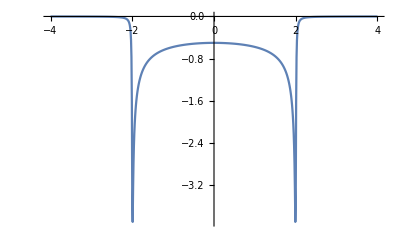

```mathematica
ListLinePlot[Table[{ω,-Im[ConjugateTranspose[IL[ω,0.01,1,0]][[1,1]]]},{ω,Range[-4,4,0.01]}],PlotRange->All]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:= Inverse[(ω+ⅈ*δ-ϵ1)IdentityMatrix[1]]
```

```mathematica
Import["/home/shardulmukim/PhD/fwi/1D/1d4imp1.csv"][[1]]
```

{0.,0.667409}

```mathematica
gdd1:= Table[{{%23[[x]]}[[1,1]],-Im[{%23[[x]]}[[1,2]][[1]]][[1,1]]},{x,1,601}]
```

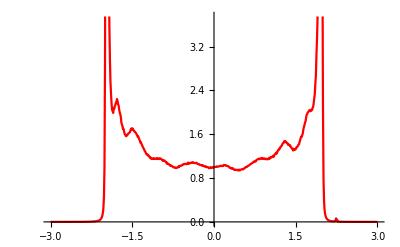

```mathematica
ListPlot[gdd1,Joined->True,PlotStyle->Red]
```

```mathematica
grr1:= Table[{{%23[[x]]}[[1,1]],-Im[{%23[[x]]}[[1,2]][[2]]][[1,1]]},{x,1,601}]
```

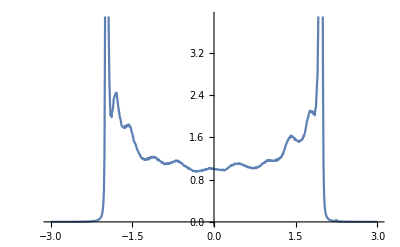

```mathematica
ListPlot[grr1,Joined->True]
```

```mathematica
GNON1:= Table[{{%23[[x]]}[[1,1]],-Im[{%23[[x]]}[[1,2]][[3]]][[1,1]]},{x,1,601}]
```

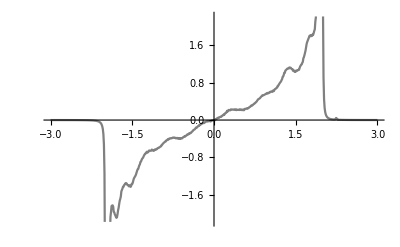

```mathematica
ListPlot[GNON1,Joined->True,PlotStyle->Gray]
```

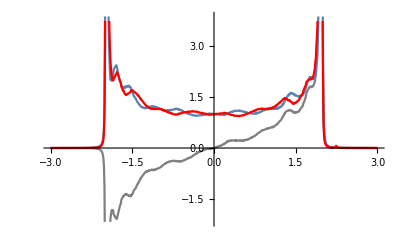

```mathematica
Show[%33,%31,%34,PlotRange->All]
```

```mathematica
set[ω_,δ_,t_,ϵ_,ϵ1_,x_,size_]:=Module[{imp1=imp[ω,δ,t,ϵ,ϵ1],imp2=imp[ω,δ,t,ϵ,0]},RandomSample[Join[RandomChoice[{imp1},x],RandomChoice[{imp2},size-x]],size]]
```

```mathematica
set[ω,δ,t,ϵ,ϵ1,10,100][[1]]
```

{{1/(ⅈ δ+ω)}}

```mathematica
Clear[set]
```

```mathematica
set[ω,δ,t,ϵ,ϵ1,1]
```

{{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}}}

```mathematica
Sum[set[0,0.01,0,0,1,5][[x]],{x,1,100}]
```

{{-4.9995-9500.05 ⅈ}}

```mathematica
c10=set[ω,δ,t,ϵ,ϵ1,10,100]
```

{{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ+ω)}},{{1/(ⅈ δ-ϵ1+ω)}},{{1/(ⅈ δ-ϵ1+ω)}}}

```mathematica
c10[[6]]
```

{{1/(ⅈ δ+ω)}}

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,x_,size_]:=Module[{c=set[ω,δ,t,ϵ,ϵ1,x,size],gg=g[ω,δ,t,ϵ],T=T1[1]},
η=Module[{},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-c[[m]].ConjugateTranspose[T].J.T].c[[m]],{m,1,size}]; J=J];
 Il1:=Inverse[IdentityMatrix[1]-sl1.T.SR[ω,δ,t,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,δ,1,0].T.sl1.T].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];{gdd1,grr1,GNON1,Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]}];
η]
```

```mathematica
tr1[0,0.01,1,0,1,10,100][[4]]
```

0.871103

```mathematica
1
```

```mathematica
Mean[Table[tr1[0,0.01,1,0,1,10,100][[4]],20000]]
```

0.578024

```mathematica
Mean[Table[tr1[0,0.01,1,0,1,10,100][[4]],25000]]
```

0.579772

```mathematica
Table[{x,Mean[Table[tr1[0,0.01,1,0,1,x,100],10000]]},{x,Range[2,22,1]}]
```

Mean::rectt: Rectangular array expected at position 1 in Mean[{{{{0.-0.709056 ⅈ}},{{0.-1.28802 ⅈ}},{{0.+0.343368 ⅈ}},0.79538},{{{0.-1.04242 ⅈ}},{{0.-0.957979 ⅈ}},{{0.+0.205936 ⅈ}},0.956205},«47»,{{{0.-1.01868 ⅈ}},{{0.-0.981477 ⅈ}},{{0.+0.287441 ⅈ}},0.917192},«9950»}].

Mean::rectt: Rectangular array expected at position 1 in Mean[{{{{0.-0.882923 ⅈ}},{{0.-1.11589 ⅈ}},{{0.-0.460953 ⅈ}},0.772765},{{{0.-0.689498 ⅈ}},{{0.-1.30739 ⅈ}},{{0.+0.576672 ⅈ}},0.568891},«47»,{{{0.-1.05992 ⅈ}},{{0.-0.94065 ⅈ}},{{0.-0.233441 ⅈ}},0.94252},«9950»}].

Mean::rectt: Rectangular array expected at position 1 in Mean[{{{{0.-0.841583 ⅈ}},{{0.-1.15682 ⅈ}},{{0.-0.492605 ⅈ}},0.730897},{{{0.-1.25991 ⅈ}},{{0.-0.742647 ⅈ}},{{0.+0.647817 ⅈ}},0.516005},«47»,{{{0.-0.800412 ⅈ}},{{0.-1.19758 ⅈ}},{{0.-0.270838 ⅈ}},0.885202},«9950»}].

General::stop: Further output of Mean::rectt will be suppressed during this calculation.

{{2,Mean[{{{{0.-0.709056 ⅈ}},{{0.-1.28802 ⅈ}},{{0.+0.343368 ⅈ}},0.79538},9998,{{{0.-1.07126 ⅈ}},{{0.-0.92942 ⅈ}},{{0.+0.221057 ⅈ}},0.946788}}]},19,{22,Mean[{1}]}}
 |  |  |  |

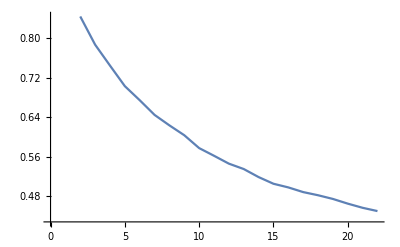

```mathematica
ListLinePlot[Table[{x,Mean[Table[tr1[0,0.01,1,0,1,x,100][[4]],10000]]},{x,Range[2,22,1]}]]
```

```mathematica
Table[{x,Mean[Table[-Im[tr1[0,0.01,1,0,1,10,100][[3]]][[1,1]],10000]]},{x,Range[2,22,1]}]
```

{{2,-0.0171806},{3,-0.0252238},{4,-0.0198108},{5,-0.0301361},{6,-0.0224984},{7,-0.029136},{8,-0.0179609},{9,-0.0230527},{10,-0.0246031},{11,-0.0176948},{12,-0.0128485},{13,-0.0297227},{14,-0.0247549},{15,-0.0230345},{16,-0.0253046},{17,-0.0217432},{18,-0.0297953},{19,-0.017147},{20,-0.0331185},{21,-0.0202558},{22,-0.0263708}}

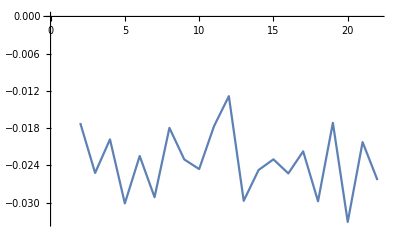

```mathematica
ListPlot[%180,Joined->True]
```

```mathematica
Table[{x,Mean[Table[-Im[tr1[0,0.01,1,0,1,10,100][[2]]][[1,1]],10000]]},{x,Range[2,22,1]}]
```

{{2,1.0056},{3,1.00746},{4,1.0075},{5,1.00574},{6,1.00559},{7,1.01498},{8,1.01531},{9,1.0091},{10,1.0067},{11,1.00113},{12,1.00865},{13,1.0155},{14,1.00584},{15,1.00989},{16,1.00963},{17,1.01125},{18,1.00573},{19,1.00215},{20,1.00071},{21,1.00311},{22,1.00987}}

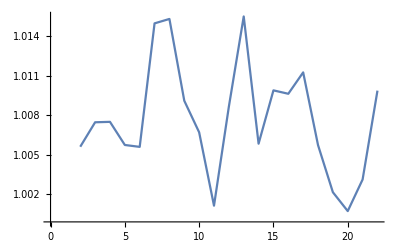

```mathematica
ListPlot[%181,Joined->True]
```

```mathematica
Table[{x,Mean[Table[-Im[tr1[0,0.01,1,0,1,10,100][[1]]][[1,1]],10000]]},{x,Range[2,22,1]}]
```

{{2,0.995086},{3,0.988245},{4,0.996285},{5,0.985039},{6,0.994374},{7,0.992176},{8,0.989864},{9,0.98858},{10,0.996624},{11,0.990271},{12,0.99042},{13,0.994548},{14,0.995545},{15,0.990397},{16,0.991626},{17,0.995039},{18,0.983635},{19,0.997939},{20,0.996817},{21,0.99779},{22,0.995976}}

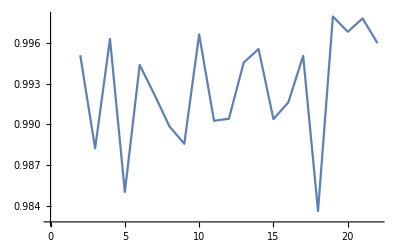

```mathematica
ListPlot[%182,Joined->True]
```

```mathematica
-Im[tr1[0,0.01,1,0,1,10,100][[3]]][[1,1]]
```

0.384194

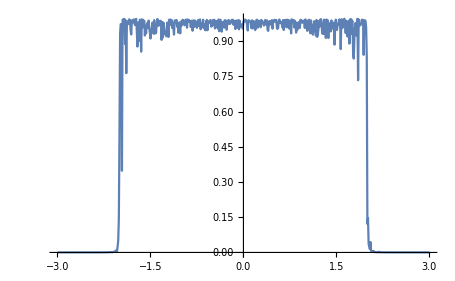

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.01,1,0,0.5,1,100]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
s[ω_,δ_,t_,ϵ_,ϵ1_,x_,size_]:=Module[{gg=g[ω,δ,t,ϵ],T=T1[1]},
η=Module[{},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[1]-set[ω,δ,t,ϵ,ϵ1,x,size][[m]].ConjugateTranspose[T].J.T].set[ω,δ,t,ϵ,ϵ1,x,size][[m]],{m,1,size}]; J=J]];η]
```

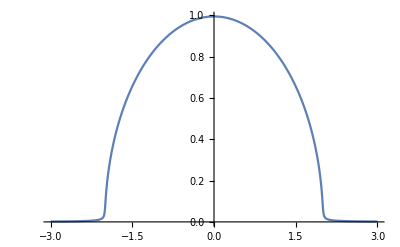

```mathematica
ListLinePlot[Table[{ω,-Im[s[ω,0.01,1,0,0,5,10]][[1,1]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
{{A^x1,A^x2}}.Inverse[{{1-1,A^(x1-x2)},{A^(-x1+x2),1-1}}].{{A^-x1},{A^-x2}}
```

{{A^(2 x1-2 x2)+A^(-2 x1+2 x2)}}

```mathematica
MatrixForm[{{0,A^(x1-x2)},{A^(-x1+x2),0}}]
```

(0 | A^(x1-x2)
A^(-x1+x2) | 0)